```mathematica
Invest[n0_,g0_]:=
Module[{n=n0,g=36/g0-1,p=0,t=0},
For[tn=0,tn<n,tn++,
p+=(1-g0/37)^(tn)*g0/37;
(*Print[(t+G)/g//N];*)
t+=(t+1)/g];
{t,p}
]
```

```mathematica
InvestTable[g0_,max0_]:=Module[{max=max0,g=g0,T={},U={},i=1},
While[Invest[i,g][[1]]<max,AppendTo[U,Invest[i,g]];i++];
U//N
]
```

```mathematica
Invest[100,1]//N
```

{15.7281,0.935423}

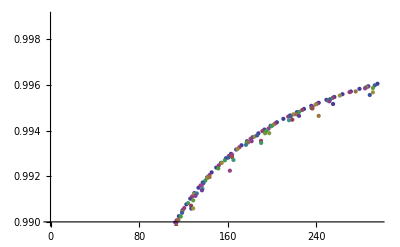

```mathematica
ListPlot[Table[InvestTable[k,300],{k,1,24,1}],PlotRange->{0.99,0.999}]
```